An ellipse E[a,b] is given at its initial position by equation:
x^2/a^2+(y-b)^2/b^2=1

The ellipse rolls without slipping along the x axis for one complete turn. Interestingly, the length of the curve generated by a focus is independent from the size of the minor axis:
F[a,b]=2 π Max[a,b]

-Graphics-

This is not true for the curve generated by the ellipse center. Let C[a,b] be the length of the curve generated by the center of the ellipse as it rolls without slipping for one turn.



You are given C[2,4]≈21.38816906.

Find C[1,4]+C[3,4]. Give your answer rounded to 8 digits behind the decimal point in the form ab.cdefghij.

椭圆E[a,b]的初始位置由以下方程给出：
x^2/a^2+(y-b)^2/b^2=1

椭圆沿着x轴无滑动地滚动一周。有趣的是，椭圆焦点的运动轨迹长度与椭圆短轴的长度无关：
F[a,b]=2 π Max[a,b]

对于椭圆中心而言则并非如此；记C[a,b]为椭圆无滑动地滚动一周时椭圆中心的运动轨迹长度。

已知C[2,4]≈21.38816906。

求C[1,4]+C[3,4]。将你的答案四舍五入到小数点后8位小数，即格式为ab.cdefghij。

设切点P的坐标是{a Cos[θ],b (1+Sin[θ])}
切线方程是(x Cos[θ])/a+((y-b) Sin[θ])/b=1
法线方程是-(x a)/Cos[θ]+((y-b) b)/Sin[θ]=b^2-a^2
过椭圆中心且平行于切线的直线方程是(x Cos[θ])/a+((y-b) Sin[θ])/b=0
它与法线的交点是{(a (a^2-b^2) Cos[θ] Sin[θ]^2)/(a^2 Sin[θ]^2+b^2 Cos[θ]^2),b-(b (a^2-b^2) Cos[θ]^2 Sin[θ])/(a^2 Sin[θ]^2+b^2 Cos[θ]^2)}
椭圆中心的参数方程是{x[θ]=b (EllipticE[1-a^2/b^2]+EllipticE[θ,1-a^2/b^2])+((a^2-b^2) Cos[θ] Sin[θ])/(√(b^2 Cos[θ]^2+a^2 Sin[θ]^2))
y[θ]=(a b)/(√(b^2 Cos[θ]^2+a^2 Sin[θ]^2))
C[a,b]=∫_(-π/2)^((3 π)/2) √(((a^2 b^2)/((b^2 Cos[θ]^2+a^2 Sin[θ]^2)^(3/2)))^2+((a b (-a^2+b^2) Cos[θ] Sin[θ])/((b^2 Cos[θ]^2+a^2 Sin[θ]^2)^(3/2)))^2)ⅆθ
=4 ((a^3 EllipticPi[1-a^4/b^4,ArcTan[(b Tan[θ])/a],1-a^2/b^2])/b^2)_(θ=-π/2)^0
=4 (a^3 EllipticPi[1-a^4/b^4,1-a^2/b^2])/b^2

```mathematica
DecimalForm[N[(4 (a^3 EllipticPi[1-a^4/b^4,1-a^2/b^2])/b^2/.{a->1,b->4})+(4 (a^3 EllipticPi[1-a^4/b^4,1-a^2/b^2])/b^2/.{a->3,b->4})],{+∞,8}]
```

44.69921807

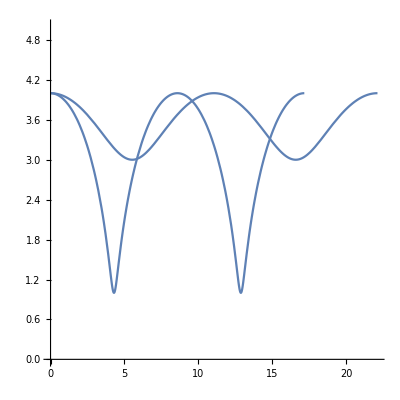

```mathematica
ParametricPlot[{b (EllipticE[1-a^2/b^2]+EllipticE[θ,1-a^2/b^2])+((a^2-b^2) Cos[θ] Sin[θ])/(√(b^2 Cos[θ]^2+a^2 Sin[θ]^2)),(a b)/(√(b^2 Cos[θ]^2+a^2 Sin[θ]^2))}/.{{a->1,b->4},{a->3,b->4}},{θ,-π/2,(3 π)/2},AspectRatio->1,PlotRange->{All,{0,5}}]
```